```mathematica
eq1=Γ Λ (1-z) (1-Λ)((1-Λ)(1-a)+a)-(1-Λ)==0
```

-1+Λ+(1-z) Γ (a+(1-a) (1-Λ)) (1-Λ) Λ==0

```mathematica
Solve[eq1, Λ]//Simplify
```

{{Λ→1},{Λ→-((-1+z) Γ+√((-1+z) Γ (4-4 a+(-1+z) Γ)))/(2 (-1+a) (-1+z) Γ)},{Λ→(Γ-z Γ+√((-1+z) Γ (4-4 a+(-1+z) Γ)))/(2 (-1+a) (-1+z) Γ)}}

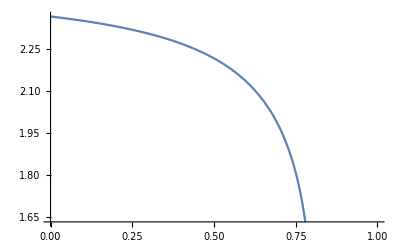

```mathematica
Plot[(Γ-z Γ+√((-1+z) Γ (4-4 a+(-1+z) Γ)))/(2 (-1+a) (-1+z) Γ)/.{Γ->8, a->3/5}, {z,0,1}]
```

```mathematica
(Γ-z Γ+√((-1+z) Γ (4-4 a+(-1+z) Γ)))/(2 (-1+a) (-1+z) Γ)/.{Γ->8, a->3/5,z->0.8}
```

1.25+2.0825×10^-8 ⅈ

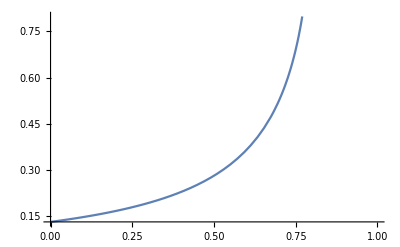

```mathematica
Plot[-((-1+z) Γ+√((-1+z) Γ (4-4 a+(-1+z) Γ)))/(2 (-1+a) (-1+z) Γ)/.{Γ->8, a->3/5}, {z,0,1}]
```

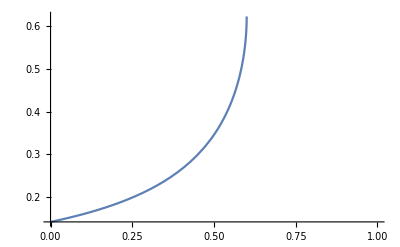

```mathematica
Plot[-((-1+z) Γ+√((-1+z) Γ (4-4 a+(-1+z) Γ)))/(2 (-1+a) (-1+z) Γ)/.{Γ->8, a->1/5}, {z,0,1}]
```

```mathematica
A=(1-Λ)((1-Λ)(1-a)+a)/.{Λ->(-((-1+z) Γ+√((-1+z) Γ (4-4 a+(-1+z) Γ)))/(2 (-1+a) (-1+z) Γ))}//Simplify
```

-(((-1+2 a) (-1+z) Γ+√((-1+z) Γ (4-4 a+(-1+z) Γ))) (Γ-z Γ+√((-1+z) Γ (4-4 a+(-1+z) Γ))))/(4 (-1+a) (-1+z)^2 Γ^2)

```mathematica
U=∫(A (1-z))ⅆz//Simplify
```

1/(4 Γ^2)(-z Γ (4+(-2+z) Γ)+√((-1+z) Γ (4-4 a+(-1+z) Γ)) (2-2 a+(-1+z) Γ)+(2 (-1+a)^2 (-Γ+√(Γ^2)) Log[2-2 a-Γ-z √(Γ^2)+√((-1+z) Γ (4-4 a+(-1+z) Γ))])/Γ+(2 (-1+a)^2 (Γ+√(Γ^2)) Log[-2+2 a+Γ-z √(Γ^2)+√((-1+z) Γ (4-4 a+(-1+z) Γ))])/Γ)

```mathematica
∫(1-z)ⅆz
```

z-z^2/2

```mathematica
UReal=1/(4 Γ^2)(-z Γ (4+(-2+z) Γ)+√((-1+z) Γ (4-4 a+(-1+z) Γ)) (2-2 a+(-1+z) Γ)+(2 (-1+a)^2 (-Γ+√(Γ^2)) Log[2-2 a-Γ-z √(Γ^2)+√((-1+z) Γ (4-4 a+(-1+z) Γ))])/Γ+(2 (-1+a)^2 (Γ+√(Γ^2)) Log[-2+2 a+Γ-z √(Γ^2)+√((-1+z) Γ (4-4 a+(-1+z) Γ))])/Γ)+const;
```

```mathematica
UReal/.{z->0}//Simplify
```

const-1/(2 Γ^2)(Γ √(Γ (-4+4 a+Γ))+2 (-Γ+√(Γ^2)) Log[-Γ+√(Γ (-4+4 a+Γ))]+(-2+a) (-Γ+√(Γ^2)) Log[2-2 a-Γ+√(Γ (-4+4 a+Γ))]-2 (Γ+√(Γ^2)) Log[Γ+√(Γ (-4+4 a+Γ))]+a (Γ+√(Γ^2)) Log[-2+2 a+Γ+√(Γ (-4+4 a+Γ))])

```mathematica
Solve[(UReal/.{z->0})==0,const]//Simplify
```

{{const→-(-((-2+2 a+Γ) √(Γ (-4+4 a+Γ)))+(2 (-1+a)^2 (-Γ+√(Γ^2)) Log[2-2 a-Γ+√(Γ (-4+4 a+Γ))])/Γ+(2 (-1+a)^2 (Γ+√(Γ^2)) Log[-2+2 a+Γ+√(Γ (-4+4 a+Γ))])/Γ)/(4 Γ^2)}}

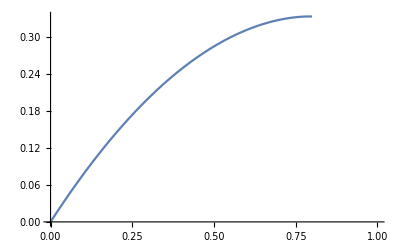

```mathematica
Plot[((1/(4 Γ^2)(-z Γ (4+(-2+z) Γ)+√((-1+z) Γ (4-4 a+(-1+z) Γ)) (2-2 a+(-1+z) Γ)+(2 (-1+a)^2 (-Γ+√(Γ^2)) Log[2-2 a-Γ-z √(Γ^2)+√((-1+z) Γ (4-4 a+(-1+z) Γ))])/Γ+(2 (-1+a)^2 (Γ+√(Γ^2)) Log[-2+2 a+Γ-z √(Γ^2)+√((-1+z) Γ (4-4 a+(-1+z) Γ))])/Γ))+(-1/(4 Γ^2)(-((-2+2 a+Γ) √(Γ (-4+4 a+Γ)))+(2 (-1+a)^2 (-Γ+√(Γ^2)) Log[2-2 a-Γ+√(Γ (-4+4 a+Γ))])/Γ+(2 (-1+a)^2 (Γ+√(Γ^2)) Log[-2+2 a+Γ+√(Γ (-4+4 a+Γ))])/Γ)))/.{Γ->8, a->3/5}, {z,0,1}]
```

```mathematica
(-1/(2 Γ^2)(-z Γ^2+Γ √((-1+z) Γ (4-4 a+(-1+z) Γ))+2 (-Γ+√(Γ^2)) Log[-Γ-z √(Γ^2)+√((-1+z) Γ (4-4 a+(-1+z) Γ))]+(-2+a) (-Γ+√(Γ^2)) Log[2-2 a-Γ-z √(Γ^2)+√((-1+z) Γ (4-4 a+(-1+z) Γ))]-2 (Γ+√(Γ^2)) Log[Γ-z √(Γ^2)+√((-1+z) Γ (4-4 a+(-1+z) Γ))]+a (Γ+√(Γ^2)) Log[-2+2 a+Γ-z √(Γ^2)+√((-1+z) Γ (4-4 a+(-1+z) Γ))])+(1/(2 Γ^2)(Γ √(Γ (-4+4 a+Γ))+2 (-Γ+√(Γ^2)) Log[-Γ+√(Γ (-4+4 a+Γ))]+(-2+a) (-Γ+√(Γ^2)) Log[2-2 a-Γ+√(Γ (-4+4 a+Γ))]-2 (Γ+√(Γ^2)) Log[Γ+√(Γ (-4+4 a+Γ))]+a (Γ+√(Γ^2)) Log[-2+2 a+Γ+√(Γ (-4+4 a+Γ))])))/.{Γ->8, a->3/5,z->0.777}
```

0.501262+0. ⅈ

```mathematica
∫_0^1 ((1/(4 Γ^2)(-z Γ (4+(-2+z) Γ)+√((-1+z) Γ (4-4 a+(-1+z) Γ)) (2-2 a+(-1+z) Γ)+(2 (-1+a)^2 (-Γ+√(Γ^2)) Log[2-2 a-Γ-z √(Γ^2)+√((-1+z) Γ (4-4 a+(-1+z) Γ))])/Γ+(2 (-1+a)^2 (Γ+√(Γ^2)) Log[-2+2 a+Γ-z √(Γ^2)+√((-1+z) Γ (4-4 a+(-1+z) Γ))])/Γ))+(-1/(4 Γ^2)(-((-2+2 a+Γ) √(Γ (-4+4 a+Γ)))+(2 (-1+a)^2 (-Γ+√(Γ^2)) Log[2-2 a-Γ+√(Γ (-4+4 a+Γ))])/Γ+(2 (-1+a)^2 (Γ+√(Γ^2)) Log[-2+2 a+Γ+√(Γ (-4+4 a+Γ))])/Γ)))ⅆz
```

$Aborted